```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"05","04"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\cylinder\1.2

05_04

```mathematica
uu=Import["uu_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
vv=Flatten[vv];

kg=Import["kg_2_26_"<>date<>".txt","Table"];
kg=Flatten[kg];
kn=Import["kn1_2_26_"<>date<>".txt","Table"];
kn=Flatten[kn];

taug=Import["taug_2_26_"<>date<>".txt","Table"];
taug=Flatten[taug];
phi=Import["phi_2_26_"<>date<>".txt","Table"];
phi=Flatten[phi];

l1=Import["l1_2_26_"<>date<>".txt","Table"];
l1=Flatten[l1];
```

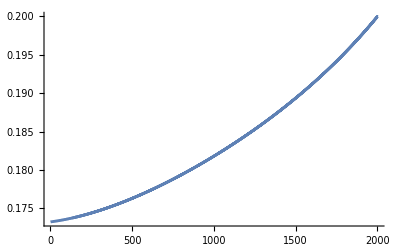

```mathematica
a1=ListLinePlot[{l1}];
a2=Plot[10^(-2),{x,0,2000}];
Show[a1,PlotRange->All]
```

```mathematica
l1;
```

```mathematica
ls1=Interpolation[l1]
```

InterpolatingFunction[…]

```mathematica
lsd=ls1'
```

InterpolatingFunction[…]

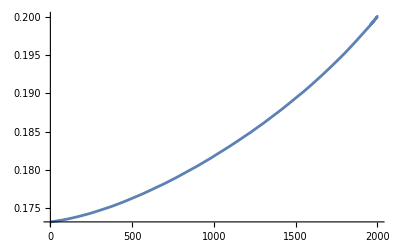

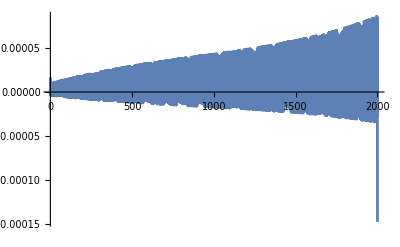

```mathematica
Plot[{ls1[x]},{x,1.,2001.},PlotRange->All]
Plot[{lsd[x]},{x,1.,2001.},PlotRange->All]
```

```mathematica
lsd/ls1
```

InterpolatingFunction[…]/InterpolatingFunction[…]

```mathematica
Show[lsd]
```

Show::gtype: InterpolatingFunction is not a type of graphics.

Show[InterpolatingFunction[…]]